```mathematica
(*definizioni mie*)
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]

(* FORSE MANCANO DEI MEZZI sommando sulle polarizzazioni?  NO!*)
```

```mathematica
μPDFpart[WmT,Q_]=(μPDFpart[Wmp,Q][#]+ μPDFpart[Wmm,Q][#])/1&
μPDFpart[WpT,Q_]=(μPDFpart[Wpp,Q][#]+ μPDFpart[Wpm,Q][#])/1&
μPDFpart[ZT,Q_]=(μPDFpart[Zp,Q][#]+ μPDFpart[Zm,Q][#])/1&
μPDFpart[γ,Q_]=(μPDFpart[γp,Q][#]+ μPDFpart[γm,Q][#])/1&

μbPDFpart[WmT,Q_]=(μbPDFpart[Wmp,Q][#]+ μbPDFpart[Wmm,Q][#])/1&
μbPDFpart[WpT,Q_]=(μbPDFpart[Wpp,Q][#]+ μbPDFpart[Wpm,Q][#])/1&
μbPDFpart[ZT,Q_]=(μbPDFpart[Zp,Q][#]+ μbPDFpart[Zm,Q][#])/1&
μbPDFpart[γ,Q_]=(μbPDFpart[γp,Q][#]+ μbPDFpart[γm,Q][#])/1&
```

(μPDFpart[Wmp,Q][#1]+μPDFpart[Wmm,Q][#1]) 1/1&

(μPDFpart[Wpp,Q][#1]+μPDFpart[Wpm,Q][#1]) 1/1&

(μPDFpart[Zp,Q][#1]+μPDFpart[Zm,Q][#1]) 1/1&

(μPDFpart[γp,Q][#1]+μPDFpart[γm,Q][#1]) 1/1&

(μbPDFpart[Wmp,Q][#1]+μbPDFpart[Wmm,Q][#1]) 1/1&

(μbPDFpart[Wpp,Q][#1]+μbPDFpart[Wpm,Q][#1]) 1/1&

(μbPDFpart[Zp,Q][#1]+μbPDFpart[Zm,Q][#1]) 1/1&

(μbPDFpart[γp,Q][#1]+μbPDFpart[γm,Q][#1]) 1/1&

```mathematica
energieQplot={1TeV, 3TeV, 10 TeV, 30 TeV};
Do[
Qplot = energieQplot[[i]];
(* LA SCALA É STOT DEL COLLIDER*)
plotmio = LogLogPlot[{
μPDFpart[μL,Qplot][x]+μPDFpart[μR,Qplot][x],
μPDFpart[γp,Qplot][x]+ μPDFpart[γm,Qplot][x],
(*μPDFpart[gp,Qplot][x]+ μPDFpart[gm,Qplot][x],*)
μPDFpart[Wmp,Qplot][x]+ μPDFpart[Wmm,Qplot][x],μPDFpart[WmL,Qplot][x],
μPDFpart[Wpp,Qplot][x]+ μPDFpart[Wpm,Qplot][x],μPDFpart[WpL,Qplot][x],
μPDFpart[Zp,Qplot][x]+ μPDFpart[Zm,Qplot][x], μPDFpart[ZL,Qplot][x]
(*μPDFpart[νμ,Qplot][x],
 μPDFpart[νeb,Qplot][x],*)
(*μPDFpart[eL,Qplot][x]+μPDFpart[eR,Qplot][x]
qPDF[x] *)
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = "<>ToString[Qplot/1000]<>" TeV"];

plotmiomuplus = LogLogPlot[{
μbPDFpart[μL,Qplot][x]+μbPDFpart[μR,Qplot][x],
μbPDFpart[γp,Qplot][x]+ μbPDFpart[γm,Qplot][x],
(*μbPDFpart[gp,Qplot][x]+ μbPDFpart[gm,Qplot][x],*)
μbPDFpart[Wmp,Qplot][x]+ μbPDFpart[Wmm,Qplot][x],μbPDFpart[WmL,Qplot][x],
μbPDFpart[Wpp,Qplot][x]+ μbPDFpart[Wpm,Qplot][x],μbPDFpart[WpL,Qplot][x],
μbPDFpart[Zp,Qplot][x]+ μbPDFpart[Zm,Qplot][x], μbPDFpart[ZL,Qplot][x]
(*μbPDFpart[νμ,Qplot][x],
 μbPDFpart[νeb,Qplot][x],*)
(*μbPDFpart[eL,Qplot][x]+μbPDFpart[eR,Qplot][x]
qPDF[x] *)
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = "<>ToString[Qplot/1000]<>" TeV"];

(* LA SCALA É STOT DEL COLLIDER PER SQRT[X]*)
plotmiov3 = LogLogPlot[{
μPDFpart[μL,Qplot Sqrt[x]][x]+μPDFpart[μR,Qplot Sqrt[x]][x],
μPDFpart[γp,Qplot Sqrt[x]][x]+ μPDFpart[γm,Qplot Sqrt[x]][x],
(*μPDFpart[gp,Qplot Sqrt[x]][x]+ μPDFpart[gm,Qplot Sqrt[x]][x],*)
μPDFpart[Wmp,Qplot Sqrt[x]][x]+ μPDFpart[Wmm,Qplot Sqrt[x]][x],μPDFpart[WmL,Qplot Sqrt[x]][x],
μPDFpart[Wpp,Qplot Sqrt[x]][x]+ μPDFpart[Wpm,Qplot Sqrt[x]][x],μPDFpart[WpL,Qplot Sqrt[x]][x],
μPDFpart[Zp,Qplot Sqrt[x]][x]+ μPDFpart[Zm,Qplot Sqrt[x]][x], μPDFpart[ZL,Qplot Sqrt[x]][x]
(*μPDFpart[νμ,Qplot Sqrt[x]][x],
 μPDFpart[νeb,Qplot Sqrt[x]][x],*)
(*μPDFpart[eL,Qplot Sqrt[x]][x]+μPDFpart[eR,Qplot Sqrt[x]][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = Sqrt[x] "<>ToString[Qplot/1000]<>" TeV"];

plotmiomuplusv3 = LogLogPlot[{
μbPDFpart[μL,Qplot Sqrt[x]][x]+μbPDFpart[μR,Qplot Sqrt[x]][x],
μbPDFpart[γp,Qplot Sqrt[x]][x]+ μbPDFpart[γm,Qplot Sqrt[x]][x],
(*μbPDFpart[gp,Qplot Sqrt[x]][x]+ μbPDFpart[gm,Qplot Sqrt[x]][x],*)
μbPDFpart[Wmp,Qplot Sqrt[x]][x]+ μbPDFpart[Wmm,Qplot Sqrt[x]][x],μbPDFpart[WmL,Qplot Sqrt[x]][x],
μbPDFpart[Wpp,Qplot Sqrt[x]][x]+ μbPDFpart[Wpm,Qplot Sqrt[x]][x],μbPDFpart[WpL,Qplot Sqrt[x]][x],
μbPDFpart[Zp,Qplot Sqrt[x]][x]+ μbPDFpart[Zm,Qplot Sqrt[x]][x], μbPDFpart[ZL,Qplot Sqrt[x]][x]
(*μbPDFpart[νμ,Qplot Sqrt[x]][x],
 μbPDFpart[νeb,Qplot Sqrt[x]][x],*)
(*μbPDFpart[eL,Qplot Sqrt[x]][x]+μbPDFpart[eR,Qplot Sqrt[x]][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = Sqrt[x] "<>ToString[Qplot/1000]<>" TeV"];


(* LA SCALA É STOT DEL COLLIDER PER [X]*)
plotmiov2 = LogLogPlot[{
μPDFpart[μL,Qplot x][x]+μPDFpart[μR,Qplot x][x],
μPDFpart[γp,Qplot x][x]+ μPDFpart[γm,Qplot x][x],
(*μPDFpart[gp,Qplot x][x]+ μPDFpart[gm,Qplot x][x],*)
μPDFpart[Wmp,Qplot x][x]+ μPDFpart[Wmm,Qplot x][x],μPDFpart[WmL,Qplot x][x],
μPDFpart[Wpp,Qplot x][x]+ μPDFpart[Wpm,Qplot x][x],μPDFpart[WpL,Qplot x][x],
μPDFpart[Zp,Qplot x][x]+ μPDFpart[Zm,Qplot x][x], μPDFpart[ZL,Qplot x][x]
(*μPDFpart[νμ,Qplot x][x],
 μPDFpart[νeb,Qplot x][x],*)
(*μPDFpart[eL,Qplot x][x]+μPDFpart[eR,Qplot x][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = x "<>ToString[Qplot/1000]<>" TeV"];

plotmiomuplusv2 = LogLogPlot[{
μbPDFpart[μL,Qplot x][x]+μbPDFpart[μR,Qplot x][x],
μbPDFpart[γp,Qplot x][x]+ μbPDFpart[γm,Qplot x][x],
(*μbPDFpart[gp,Qplot x][x]+ μbPDFpart[gm,Qplot x][x],*)
μbPDFpart[Wmp,Qplot x][x]+ μbPDFpart[Wmm,Qplot x][x],μbPDFpart[WmL,Qplot x][x],
μbPDFpart[Wpp,Qplot x][x]+ μbPDFpart[Wpm,Qplot x][x],μbPDFpart[WpL,Qplot x][x],
μbPDFpart[Zp,Qplot x][x]+ μbPDFpart[Zm,Qplot x][x], μbPDFpart[ZL,Qplot x][x]
(*μbPDFpart[νμ,Qplot x][x],
 μbPDFpart[νeb,Qplot x][x],*)
(*μbPDFpart[eL,Qplot x][x]+μbPDFpart[eR,Qplot x][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = x "<>ToString[Qplot/1000]<>" TeV"];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu-scaleQ.pdf",plotmio ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu+scaleQ.pdf",plotmiomuplus ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu-scaleQx.pdf",plotmiov2 ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu+scaleQx.pdf",plotmiomuplusv2 ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu-scaleQsqrtx.pdf",plotmiov3 ];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/alltogether/"<>ToString[Qplot/1000]<>"TeV_mu+scaleQsqrtx.pdf",plotmiomuplusv3 ]



,{i,1,Length[energieQplot]}]
```

InterpolatingFunction::dmval: Input value {-0.109706} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
TeV
ToString[Qplot/1000]<>"TeV_mu-scaleQ.pdf"
```

1000

30TeV_mu-scaleQ.pdf

```mathematica
(*valore usato nei primi test alpha=1/137.*)
(*alpha in realtà runna nelle PDF!!!!!*)
alpha= 0.00783581(*Initial condition in LePDF at MW*)
e=Sqrt[4Pi alpha]
MZ=91.1876
MW=80.379(* come nei run di MG5 e non 80.379*)
cw=Sqrt[MW^2/MZ^2]
sw=Sqrt[1-cw^2]
g=e/sw
mmu=0.1056584
```

0.00783581

0.313796

91.1876

80.379

0.881469

0.472243

0.664479

0.105658

```mathematica
(*gV=.
gL=.
gR=.
gt=.
MV=.*)
```

```mathematica
rulesW={(*gV->1/2*)gV->1,gL->1,gR->0,gt->g/Sqrt[2],MV->MW}

μLEVApart[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesW(*2.7 a*)
μLEVApart[Wmm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2]/.rulesW (*2.7 b*)
μLEVApart[WmL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesW(*2.7 c*)

μREVApart[Wmp,Q_,x_]:=(gR^2/gL^2) μLEVApart[Wmm,Q,x] /.rulesW(*2.7 d*)
μREVApart[Wmm,Q_,x_]:=(gR^2/gL^2) μLEVApart[Wmp,Q,x] /.rulesW(*2.7 e*)
μREVApart[WmL,Q_,x_]:=(gR^2/gL^2) μLEVApart[WmL,Q,x] /.rulesW(*2.7 f*)


μEVApart[Wmp,Q_,x_]:=(μLEVApart[Wmp,Q,x]+μREVApart[Wmp,Q,x])/2
μEVApart[Wmm,Q_,x_]:=(μLEVApart[Wmm,Q,x]+μREVApart[Wmm,Q,x])/2
μEVApart[WmL,Q_,x_]:=(μLEVApart[WmL,Q,x]+μREVApart[WmL,Q,x])/2


(*Scale as LEPDF EVA*)

μLEVApartv2[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(mmu^2+MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesW(*2.7 a*)
μLEVApartv2[Wmm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(mmu^2+MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesW (*2.7 b*)
μLEVApartv2[WmL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)(Q^2)/(Q^2+(1-x)MV^2)/.rulesW(*2.7 c*)

μREVApartv2[Wmp,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[Wmm,Q,x] /.rulesW(*2.7 d*)
μREVApartv2[Wmm,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[Wmp,Q,x] /.rulesW(*2.7 e*)
μREVApartv2[WmL,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[WmL,Q,x] /.rulesW(*2.7 f*)


μEVApartv2[Wmp,Q_,x_]:=(μLEVApartv2[Wmp,Q,x]+μREVApartv2[Wmp,Q,x])/2
μEVApartv2[Wmm,Q_,x_]:=(μLEVApartv2[Wmm,Q,x]+μREVApartv2[Wmm,Q,x])/2
μEVApartv2[WmL,Q_,x_]:=(μLEVApartv2[WmL,Q,x]+μREVApartv2[WmL,Q,x])/2
```

{gV→1,gL→1,gR→0,gt→0.469858,MV→80.379}

```mathematica
(*

EVA RICHARD:


 Log[Q^2/MV^2]

*)


(*

EVA DAVID:


 (Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  

*)
```

10000

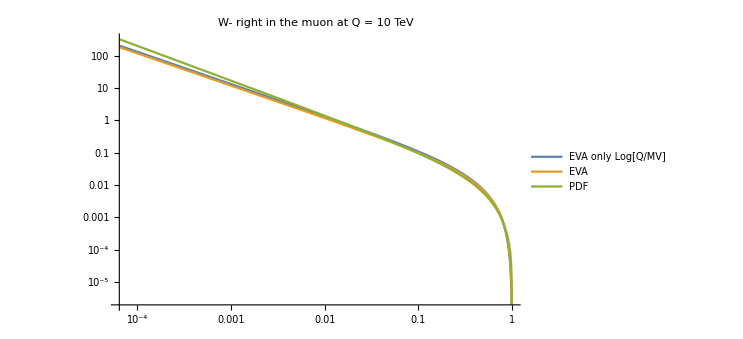

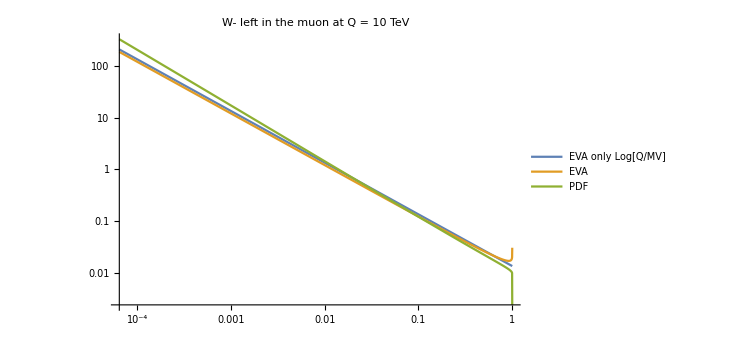

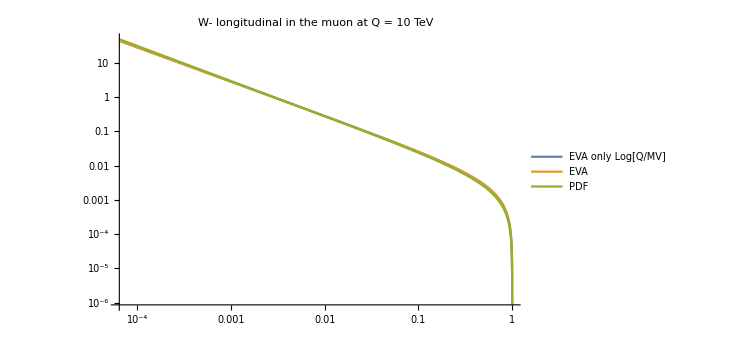

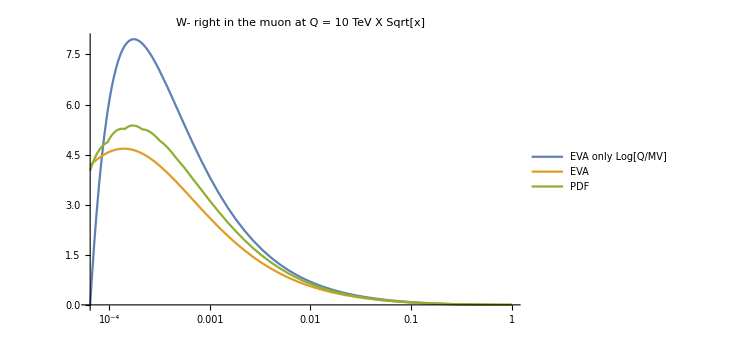

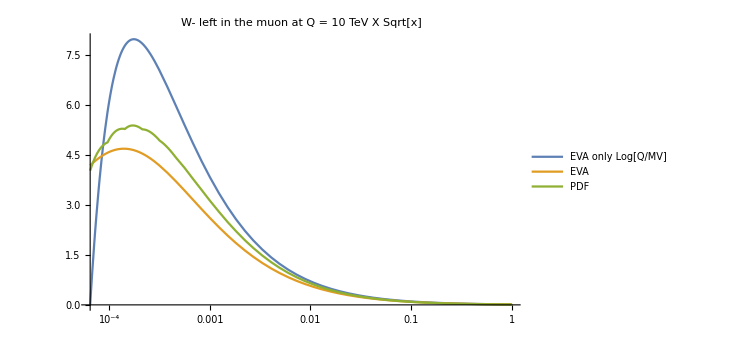

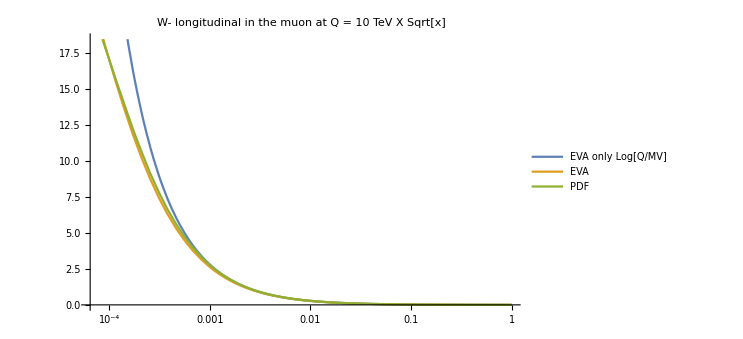

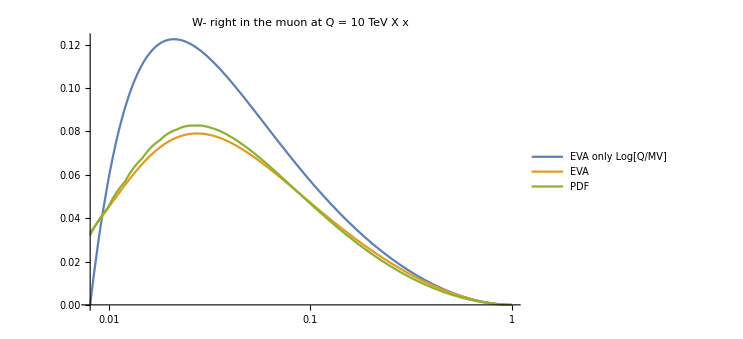

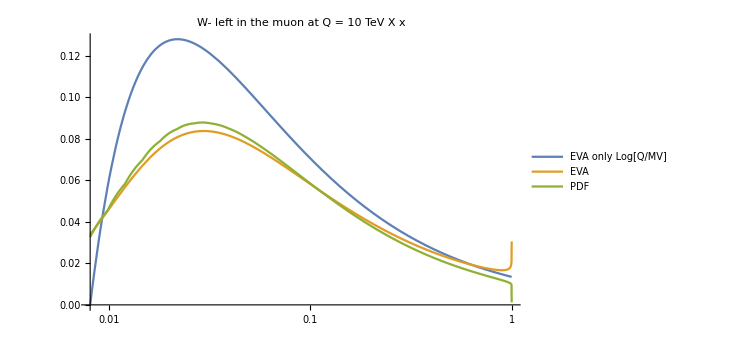

```mathematica
Q=10000


LogLogPlot[{μEVApart[Wmp,Q ,x],μEVApartv2[Wmp,Q ,x],μPDFpart[Wmp,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[Wmm,Q ,x],μEVApartv2[Wmm,Q ,x],μPDFpart[Wmm,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[WmL,Q ,x],μEVApartv2[WmL,Q ,x],μPDFpart[WmL,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]

LogLinearPlot[{μEVApart[Wmp,Q Sqrt[x],x],μEVApartv2[Wmp,Q Sqrt[x],x],μPDFpart[Wmp,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Wmm,Q Sqrt[x],x],μEVApartv2[Wmm,Q Sqrt[x],x],μPDFpart[Wmm,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[WmL,Q Sqrt[x],x],μEVApartv2[WmL,Q Sqrt[x],x],μPDFpart[WmL,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]


LogLinearPlot[{μEVApart[Wmp,Q x,x],μEVApartv2[Wmp,Q x,x],μPDFpart[Wmp,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Wmm,Q x,x],μEVApartv2[Wmm,Q x,x],μPDFpart[Wmm,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[WmL,Q x,x],μEVApartv2[WmL,Q x,x],μPDFpart[WmL,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

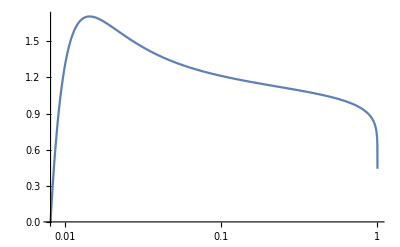

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q x ,x]/μEVApartv2[Wmp,Q x,x]},{x,(MW/Q),1}]
```

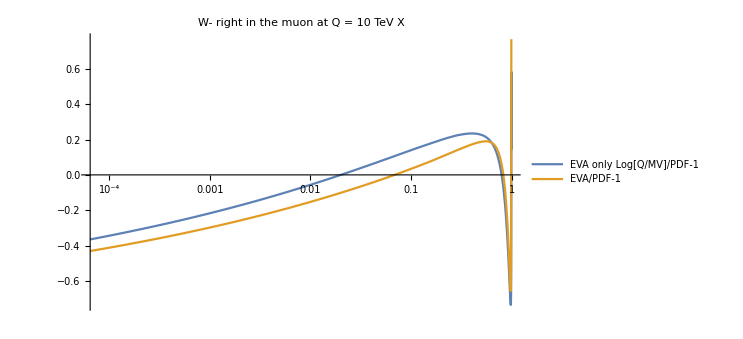

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q ][x]-1,μEVApartv2[Wmp,Q ,x]/μPDFpart[Wmp,Q ][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X ",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

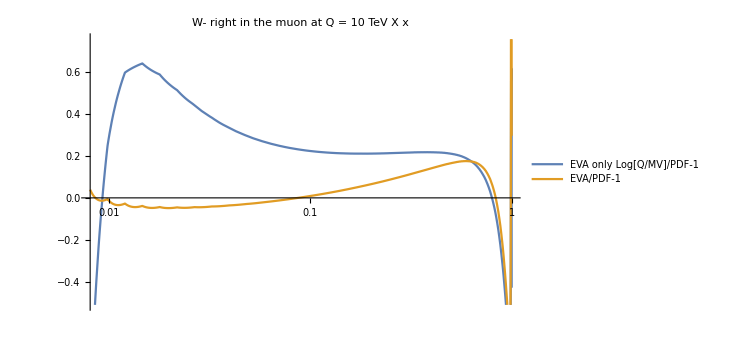

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q x,x]/μPDFpart[Wmp,Q x][x]-1,μEVApartv2[Wmp,Q x,x]/μPDFpart[Wmp,Q x][x]-1},{x,(MW/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

```mathematica
(*μLEVApartv2[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesW(*2.7 a*)*)
```

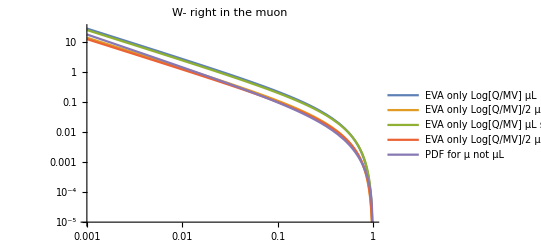

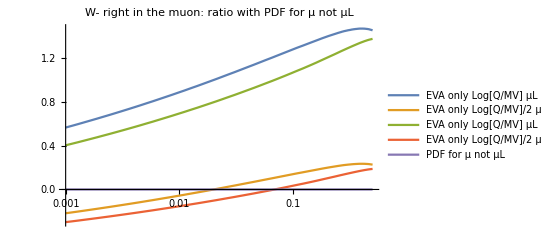

```mathematica
LogLogPlot[{μLEVApart[Wmp,Q ,x],μLEVApart[Wmp,Q ,x]/2,μLEVApartv2[Wmp,Q,x],μLEVApartv2[Wmp,Q,x]/2,μPDFpart[Wmp,Q][x]},{x,0.001,1},PlotLegends->{"EVA only Log[Q/MV] μL ","EVA only Log[Q/MV]/2 μL ","EVA only Log[Q/MV] μL scale as David","EVA only Log[Q/MV]/2 μL scale as David ","PDF for μ not μL"},PlotLabel->"W- right in the muon"]
LogLinearPlot[{μLEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q][x]-1,μLEVApart[Wmp,Q ,x]/2/μPDFpart[Wmp,Q][x]-1,μLEVApartv2[Wmp,Q,x]/μPDFpart[Wmp,Q][x]-1,μLEVApartv2[Wmp,Q,x]/2/μPDFpart[Wmp,Q][x]-1,μPDFpart[Wmp,Q][x]/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5},PlotLegends->{"EVA only Log[Q/MV] μL ","EVA only Log[Q/MV]/2 μL ","EVA only Log[Q/MV] μL scale as David","EVA only Log[Q/MV]/2 μL scale as David ","PDF for μ not μL"},PlotLabel->"W- right in the muon: ratio with PDF for μ not μL"]

(*LogLogPlot[{ μEVApart[Wmp,Q ,x],μPDFpart[Wmp,Q][x]},{x,0.001,0.5}]
LogLinearPlot[{ μEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{ (μEVApart[Wmp,Sqrt[Q ^2+MW^2(1-x)]/Sqrt[(1-x) /Exp[Q^2/(Q^2+(1-x)MW^2)]],x])/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{μEVApart[Wmm,Q ,x]/μPDFpart[Wmm,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{(μEVApart[Wmp,Q ,x]+μEVApart[Wmm,Q ,x])/μPDFpart[WmT,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{μEVApart[WmL,Q ,x]/μPDFpart[WmL,Q][x]-1},{x,0.001,0.5}]*)
```

```mathematica
(*Plot di Debug*)
```

```mathematica
(-1/2)-(-1)*sw^2
```

-0.276987

```mathematica
(*!!!!!!!  !!!!!!!!*)
```

```mathematica
rulesZfL={(*gV->1/2*(-1/2)-(-1)sw^2,*)gV->1,gL->(-1/2)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}
rulesZfR={(*gV->1/2*(0)-(-1)sw^2,*)gV->1,gL->(0)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}

μLEVApart[Zp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesZfL(*2.7 a*)
μLEVApart[Zm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2]/.rulesZfL (*2.7 b*)
μLEVApart[ZL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesZfL(*2.7 c*)

μREVApart[Zp,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2] /.rulesZfR(*2.7 d*)
μREVApart[Zm,Q_,x_]:=(gR^2/gL^2) gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesZfR(*2.7 e*)
μREVApart[ZL,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 (1-x)/(x) /.rulesZfR(*2.7 f*)

μEVApart[Zp,Q_,x_]:=(μLEVApart[Zp,Q,x]+μREVApart[Zp,Q,x])/2




μEVApart[Zm,Q_,x_]:=(μLEVApart[Zm,Q,x]+μREVApart[Zm,Q,x])/2



μEVApart[ZL,Q_,x_]:=(μLEVApart[ZL,Q,x]+μREVApart[ZL,Q,x])/2



(*Scale as LEPDF EVA*)

rulesZfL={(*gV->1/2*(-1/2)-(-1)sw^2,*)gV->1,gL->(-1/2)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}
rulesZfR={(*gV->1/2*(0)-(-1)sw^2,*)gV->1,gL->(0)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}

μLEVApartv2[Zp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(mmu^2+MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfL(*2.7 a*)
μLEVApartv2[Zm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(mmu^2+MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesZfL (*2.7 b*)
μLEVApartv2[ZL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)(Q^2)/(Q^2+(1-x)MV^2)/.rulesZfL(*2.7 c*)

μREVApartv2[Zp,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(mmu^2+MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfR(*2.7 d*)
μREVApartv2[Zm,Q_,x_]:=(gR^2/gL^2) gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(mmu^2+MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfR(*2.7 e*)
μREVApartv2[ZL,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)(Q^2)/(Q^2+(1-x)MV^2) /.rulesZfR(*2.7 f*)

μEVApartv2[Zp,Q_,x_]:=(μLEVApartv2[Zp,Q,x]+μREVApartv2[Zp,Q,x])/2




μEVApartv2[Zm,Q_,x_]:=(μLEVApartv2[Zm,Q,x]+μREVApartv2[Zm,Q,x])/2



μEVApartv2[ZL,Q_,x_]:=(μLEVApartv2[ZL,Q,x]+μREVApartv2[ZL,Q,x])/2






μEVApart[Zp,Q,x]
```

{gV→1,gL→-0.276987,gR→0.223013,gt→0.753832,MV→91.1876}

{gV→1,gL→0.223013,gR→0.223013,gt→0.753832,MV→91.1876}

{gV→1,gL→-0.276987,gR→0.223013,gt→0.753832,MV→91.1876}

{gV→1,gL→0.223013,gR→0.223013,gt→0.753832,MV→91.1876}

1/2 (0.00336287/x+(0.00518761 (1-x)^2)/x)

3000

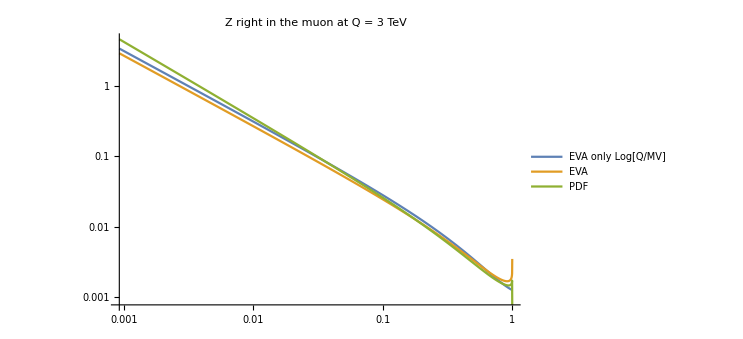

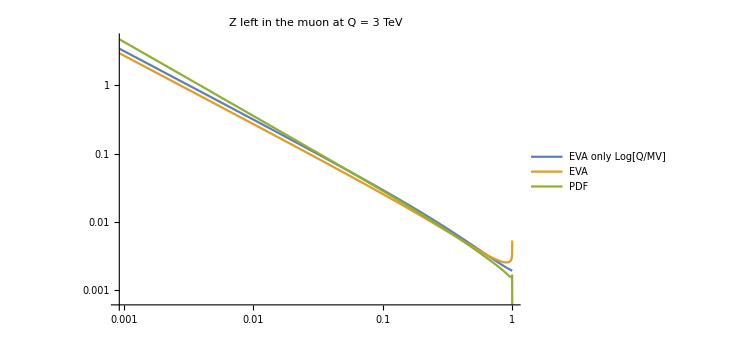

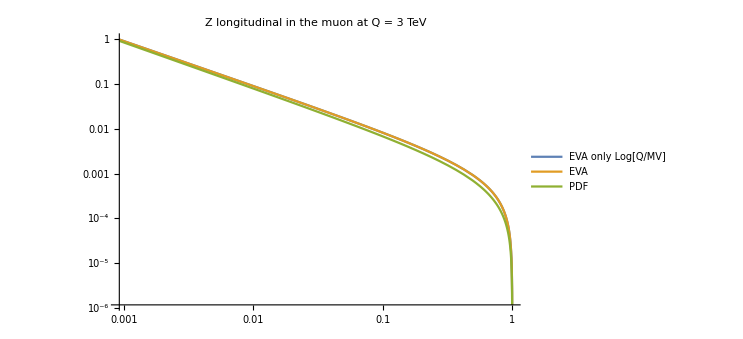

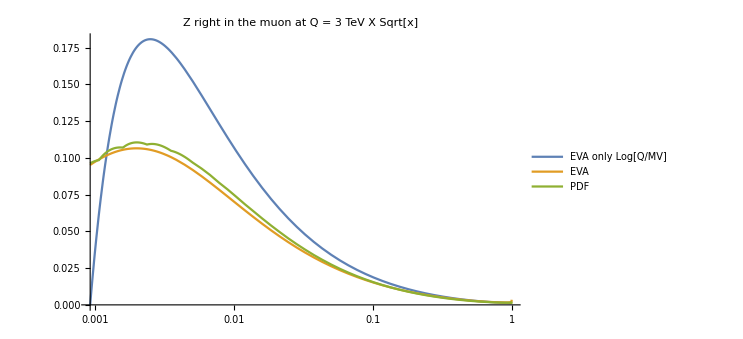

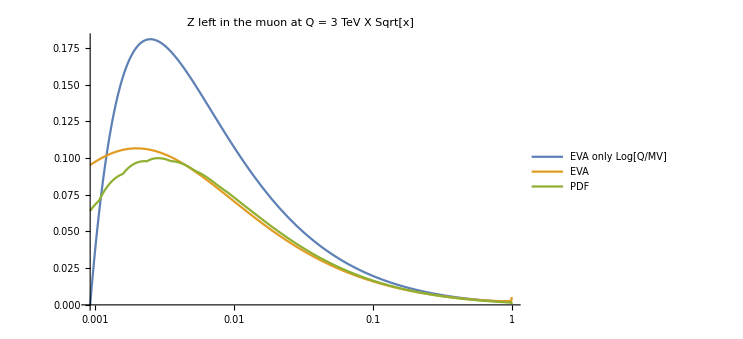

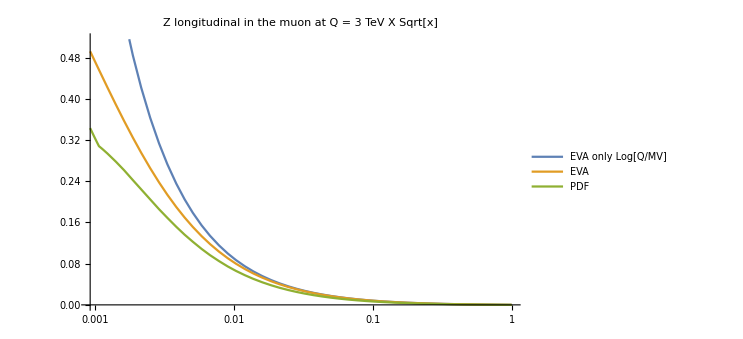

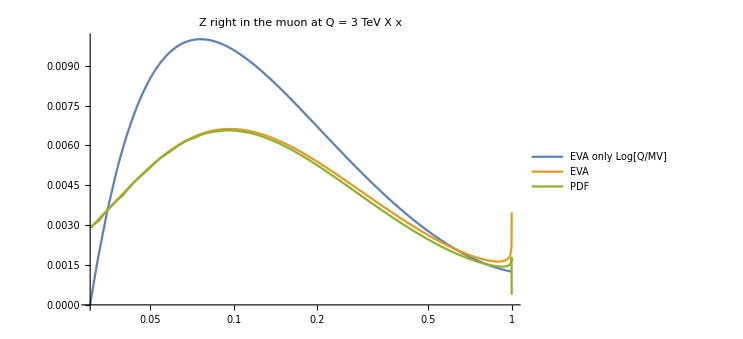

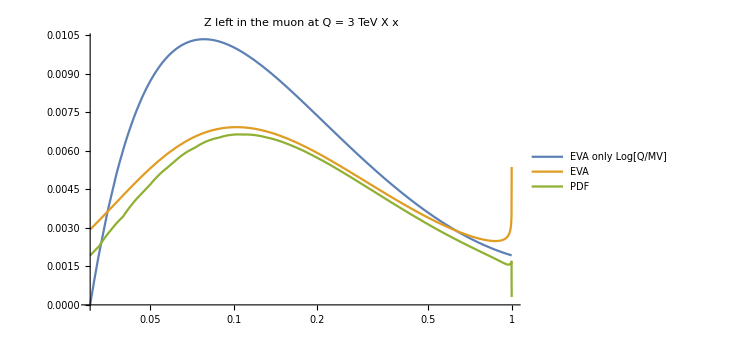

```mathematica
Q=3000

LogLogPlot[{μEVApart[Zp,Q ,x],μEVApartv2[Zp,Q ,x],μPDFpart[Zp,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[Zm,Q ,x],μEVApartv2[Zm,Q ,x],μPDFpart[Zm,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLogPlot[{μEVApart[ZL,Q ,x],μEVApartv2[ZL,Q ,x],μPDFpart[ZL,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]


LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x],μEVApartv2[Zp,Q Sqrt[x],x],μPDFpart[Zp,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Zm,Q Sqrt[x],x],μEVApartv2[Zm,Q Sqrt[x],x],μPDFpart[Zm,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[ZL,Q Sqrt[x],x],μEVApartv2[ZL,Q Sqrt[x],x],μPDFpart[ZL,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]


LogLinearPlot[{μEVApart[Zp,Q x,x],μEVApartv2[Zp,Q x,x],μPDFpart[Zp,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[Zm,Q x,x],μEVApartv2[Zm,Q x,x],μPDFpart[Zm,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
LogLinearPlot[{μEVApart[ZL,Q x,x],μEVApartv2[ZL,Q x,x],μPDFpart[ZL,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EVA only Log[Q/MV]","EVA","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550]
```

```mathematica
plotstyle={Thick,Thick,{Black,Dashed},{Black,DotDashed}}
```

{Thickness[Large],Thickness[Large],{GrayLevel[0],Dashing[{Small,Small}]},{GrayLevel[0],Dashing[{0,Small,Small,Small}]}}

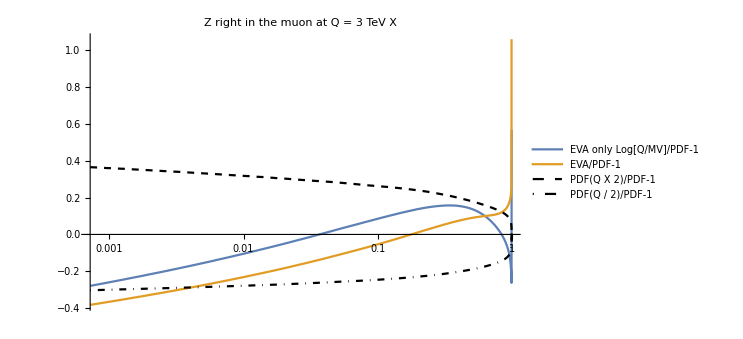

```mathematica
LogLinearPlot[{μEVApart[Zp,Q ,x]/μPDFpart[Zp,Q ][x]-1,μEVApartv2[Zp,Q ,x]/μPDFpart[Zp,Q ][x]-1,μPDFpart[Zp,Q *2][x]/μPDFpart[Zp,Q ][x]-1,μPDFpart[Zp,Q /2][x]/μPDFpart[Zp,Q ][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X ",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle]
```

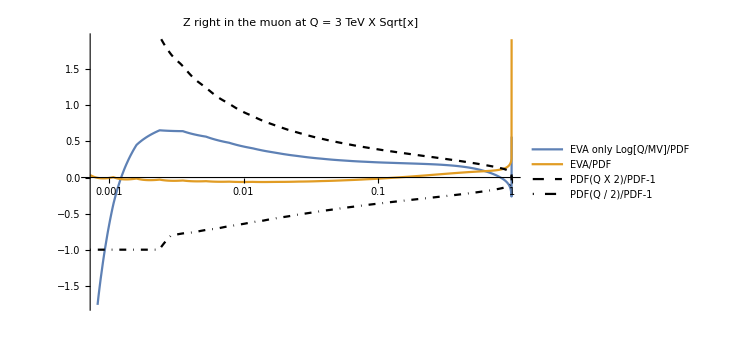

```mathematica
LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μEVApartv2[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μPDFpart[Zp,Q Sqrt[x]*2][x]/μPDFpart[Zp,Q Sqrt[x] ][x]-1,μPDFpart[Zp,Q Sqrt[x]/2][x]/μPDFpart[Zp,Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF","EVA/PDF","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle]
```

```mathematica
(*DEFINIZIONE: μbPDFpart[part_,Q_][x_]:=μPDFpart[CP[part],Q][x]*)
μbEVApart[part_,Q_,x_]:=μEVApart[CP[part],Q,x]
μbEVApartv2[part_,Q_,x_]:=μEVApartv2[CP[part],Q,x]

μEVApart[ZT,Q_,x_]:=μEVApart[Zp,Q,x]+μEVApart[Zm,Q,x]
μbEVApart[ZT,Q_,x_]:=μbEVApart[Zp,Q,x]+μbEVApart[Zm,Q,x]

μEVApart[WpT,Q_,x_]:=μEVApart[Wpp,Q,x]+μEVApart[Wpm,Q,x]
μbEVApart[WpT,Q_,x_]:=μbEVApart[Wpp,Q,x]+μbEVApart[Wpm,Q,x]
μEVApart[WmT,Q_,x_]:=μEVApart[Wmp,Q,x]+μEVApart[Wmm,Q,x]
μbEVApart[WmT,Q_,x_]:=μbEVApart[Wmp,Q,x]+μbEVApart[Wmm,Q,x]


μEVApartv2[ZT,Q_,x_]:=μEVApartv2[Zp,Q,x]+μEVApartv2[Zm,Q,x]
μbEVApartv2[ZT,Q_,x_]:=μbEVApartv2[Zp,Q,x]+μbEVApartv2[Zm,Q,x]

μEVApartv2[WpT,Q_,x_]:=μEVApartv2[Wpp,Q,x]+μEVApartv2[Wpm,Q,x]
μbEVApartv2[WpT,Q_,x_]:=μbEVApartv2[Wpp,Q,x]+μbEVApartv2[Wpm,Q,x]
μEVApartv2[WmT,Q_,x_]:=μEVApartv2[Wmp,Q,x]+μEVApartv2[Wmm,Q,x]
μbEVApartv2[WmT,Q_,x_]:=μbEVApartv2[Wmp,Q,x]+μbEVApartv2[Wmm,Q,x]
```

```mathematica
listanomi={ZT,Zp,Zm,ZL,WmT,Wmp,Wpp,WmL}
listanomichiari={"Z_T","Z_R","Z_L-","Z_0","W-_T","W-_R","W-_L","W-_0"}
listaenergie={1000,3000,10000,30000}

Do[
Q=listaenergie[[k]];
Do[plotratioPDFsqrtx[i]=LogLinearPlot[{μEVApart[listanomi[[i]],Q Sqrt[x],x]/μPDFpart[listanomi[[i]],Q Sqrt[x]][x]-1,μEVApartv2[listanomi[[i]],Q Sqrt[x],x]/μPDFpart[listanomi[[i]],Q Sqrt[x]][x]-1,μPDFpart[listanomi[[i]],Q Sqrt[x]*2][x]/μPDFpart[listanomi[[i]],Q Sqrt[x] ][x]-1,μPDFpart[listanomi[[i]],Q Sqrt[x]/2][x]/μPDFpart[listanomi[[i]],Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/ratios/"<>ToString[Q/1000]<>"TeV/"<>listanomichiari[[i]]<>"_Qsqrtx.pdf",plotratioPDFsqrtx[i] ];

plotratioPDFx[i]=LogLinearPlot[{μEVApart[listanomi[[i]],Q  x,x]/μPDFpart[listanomi[[i]],Q  x][x]-1,μEVApartv2[listanomi[[i]],Q  x,x]/μPDFpart[listanomi[[i]],Q  x][x]-1,μPDFpart[listanomi[[i]],Q  x*2][x]/μPDFpart[listanomi[[i]],Q  x ][x]-1,μPDFpart[listanomi[[i]],Q  x/2][x]/μPDFpart[listanomi[[i]],Q  x][x]-1},{x,(MW/Q),1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV X x",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/ratios/"<>ToString[Q/1000]<>"TeV/"<>listanomichiari[[i]]<>"_Qx.pdf",plotratioPDFx[i] ];

plotratioPDF[i]=LogLinearPlot[{μEVApart[listanomi[[i]],Q   ,x]/μPDFpart[listanomi[[i]],Q   ][x]-1,μEVApartv2[listanomi[[i]],Q   ,x]/μPDFpart[listanomi[[i]],Q   ][x]-1,μPDFpart[listanomi[[i]],Q   *2][x]/μPDFpart[listanomi[[i]],Q    ][x]-1,μPDFpart[listanomi[[i]],Q   /2][x]/μPDFpart[listanomi[[i]],Q   ][x]-1},{x,0.001,1},PlotLegends->{"EVA only Log[Q/MV]/PDF-1","EVA/PDF-1","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle];

Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotPDFs/ratios/"<>ToString[Q/1000]<>"TeV/"<>listanomichiari[[i]]<>"_Q.pdf",plotratioPDF[i] ];

,{i,1, Length[listanomi]}]

,{k,1, Length[listaenergie]}
]
```

{ZT,Zp,Zm,ZL,WmT,Wmp,Wpp,WmL}

{Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0}

{1000,3000,10000,30000}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {26.4993} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

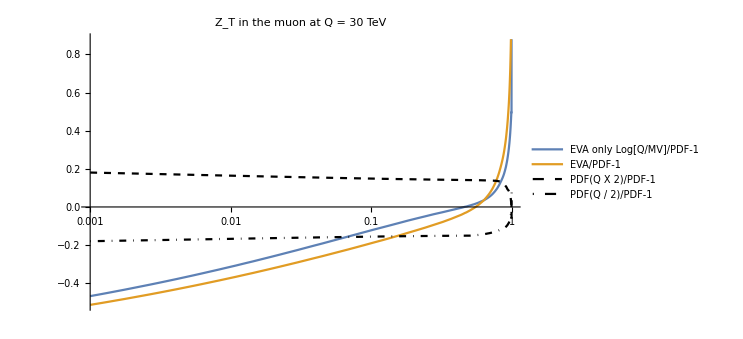

```mathematica
plotratioPDF[1]
```

```mathematica
PLOTPTOVA[2]
```

PLOTPTOVA[2]

Part::partw: Part 56 of {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0} does not exist.

StringJoin::string: String expected at position 1 in {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0}⟦56⟧<> in the muon at Q = 30 TeV X Sqrt[x].

Part::partw: Part 56 of {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0} does not exist.

StringJoin::string: String expected at position 1 in {Z_T,Z_R,Z_L-,Z_0,W-_T,W-_R,W-_L,W-_0}⟦56⟧<> in the muon at Q = 30 TeV X Sqrt[x].

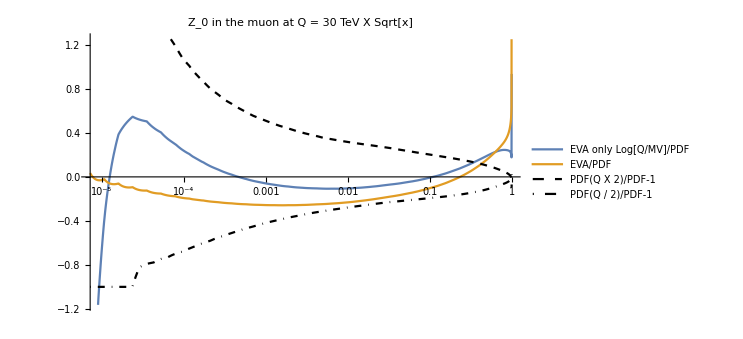

```mathematica
LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μEVApartv2[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μPDFpart[Zp,Q Sqrt[x]*2][x]/μPDFpart[Zp,Q Sqrt[x] ][x]-1,μPDFpart[Zp,Q Sqrt[x]/2][x]/μPDFpart[Zp,Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EVA only Log[Q/MV]/PDF","EVA/PDF","PDF(Q X 2)/PDF-1","PDF(Q / 2)/PDF-1"},PlotLabel->listanomichiari[[i]]<>" in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]",BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotStyle->plotstyle]/.i->4
```

```mathematica
(*NEL NOTEBOOK ORIGINARIO LA SCALA era mμμ/2 nella funzione *)
```

```mathematica
(*DEFINIZIONE FUNZIONI CON mμμ e scala PDF vincolate*)
Lμmμp[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μPDFpart[part1,mμμ][x]μbPDFpart[part2,mμμ][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
(*LμmμpNpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),Lμmμp[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0]},{i,1,Npoints}]*)
LμmμpNpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,Lμmμp[part1,part2,  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,sqrts0]},{i,1,Npoints}]
```

```mathematica
(*DEFINIZIONE FUNZIONI CON mμμ e scala PDF legate da muovermμμ*)
```

```mathematica
Lμmμpscale[part1_,part2_,mμμ_,sqrts0_,muovermμμ_]:=NIntegrate[1/x μPDFpart[part1,mμμ*muovermμμ][x]μbPDFpart[part2,mμμ*muovermμμ][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
(*LμmμpNpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),Lμmμpscale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]*)
LμmμpNpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,Lμmμpscale[part1,part2,  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
LμmμpEVAscale[part1_,part2_,mμμ_,sqrts0_,muovermμμ_]:=NIntegrate[1/x μEVApart[part1,mμμ*muovermμμ,x]μbEVApart[part2,mμμ*muovermμμ,mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
(*LμmμpEVANpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVAscale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]*)
LμmμpEVANpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,LμmμpEVAscale[part1,part2,  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
LμmμpEVAv2scale[part1_,part2_,mμμ_,sqrts0_,muovermμμ_]:=NIntegrate[1/x μEVApartv2[part1,mμμ*muovermμμ,x]μbEVApartv2[part2,mμμ*muovermμμ,mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
(*LμmμpEVAv2Npointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVAv2scale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]*)
LμmμpEVAv2Npointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,LμmμpEVAv2scale[part1,part2,  mμμ+Exp[ (i-1) Log[(sqrts0-mμμ)]/(Npoints-1)]-1,sqrts0,muovermμμ]},{i,1,Npoints}]
```

{{WmT,WpT},{WmL,WpL},{WmL,WpT},{WmT,WpL},{ZT,ZT},{ZL,ZL},{ZL,ZT},{ZT,ZL},{Wmm,Wpm},{Wmm,Wpp},{Wmp,Wpm},{Wmp,Wpp},{Zm,Zm},{Zm,Zm},{Zp,Zm},{Zp,Zp}}

{1000,3000,10000,30000}

30000

0.5

2

{{200,0.526985},{199+2^(1/13) 5^(2/39) 149^(1/39),0.526442},{199+2^(2/13) 5^(4/39) 149^(2/39),0.525735},{199+2^(3/13) 5^(2/13) 149^(1/13),0.524814},{199+2^(4/13) 5^(8/39) 149^(4/39),0.523612},{199+2^(5/13) 5^(10/39) 149^(5/39),0.522045},{199+2^(6/13) 5^(4/13) 149^(2/13),0.520002},{199+2^(7/13) 5^(14/39) 149^(7/39),0.517336},{199+2^(8/13) 5^(16/39) 149^(8/39),0.513859},{199+2^(9/13) 5^(6/13) 149^(3/13),0.509325},{199+2^(10/13) 5^(20/39) 149^(10/39),0.503418},{199+2^(11/13) 5^(22/39) 149^(11/39),0.495736},{199+2^(12/13) 5^(8/13) 149^(4/13),0.485778},{199+2 5^(2/3) 149^(1/3),0.47294},{199+2 2^(1/13) 5^(28/39) 149^(14/39),0.456525},{199+2 2^(2/13) 5^(10/13) 149^(5/13),0.431872},{199+2 2^(3/13) 5^(32/39) 149^(16/39),0.402204},{199+2 2^(4/13) 5^(34/39) 149^(17/39),0.367413},{199+2 2^(5/13) 5^(12/13) 149^(6/13),0.32317},{199+2 2^(6/13) 5^(38/39) 149^(19/39),0.275469},{199+10 2^(7/13) 5^(1/39) 149^(20/39),0.223325},{199+10 2^(8/13) 5^(1/13) 149^(7/13),0.172985},{199+10 2^(9/13) 5^(5/39) 149^(22/39),0.127143},{199+10 2^(10/13) 5^(7/39) 149^(23/39),0.0883451},{199+10 2^(11/13) 5^(3/13) 149^(8/13),0.0583279},{199+10 2^(12/13) 5^(11/39) 149^(25/39),0.036705},{199+20 5^(1/3) 149^(2/3),0.0220985},{199+20 2^(1/13) 5^(5/13) 149^(9/13),0.0127733},{199+20 2^(2/13) 5^(17/39) 149^(28/39),0.007108},{199+20 2^(3/13) 5^(19/39) 149^(29/39),0.00381403},{199+20 2^(4/13) 5^(7/13) 149^(10/13),0.00197166},{199+20 2^(5/13) 5^(23/39) 149^(31/39),0.00097854},{199+20 2^(6/13) 5^(25/39) 149^(32/39),0.000462917},{199+20 2^(7/13) 5^(9/13) 149^(11/13),0.000206183},{199+20 2^(8/13) 5^(29/39) 149^(34/39),0.0000846599},{199+20 2^(9/13) 5^(31/39) 149^(35/39),0.0000308708},{199+20 2^(10/13) 5^(11/13) 149^(12/13),9.30171×10^-6},{199+20 2^(11/13) 5^(35/39) 149^(37/39),1.96678×10^-6},{199+20 2^(12/13) 5^(37/39) 149^(38/39),1.72967×10^-7},{29999,1.4145×10^-19}}

{{200,0.550422},{199+2^(1/13) 5^(2/39) 149^(1/39),0.549804},{199+2^(2/13) 5^(4/39) 149^(2/39),0.548997},{199+2^(3/13) 5^(2/13) 149^(1/13),0.547944},{199+2^(4/13) 5^(8/39) 149^(4/39),0.546569},{199+2^(5/13) 5^(10/39) 149^(5/39),0.544774},{199+2^(6/13) 5^(4/13) 149^(2/13),0.542427},{199+2^(7/13) 5^(14/39) 149^(7/39),0.539358},{199+2^(8/13) 5^(16/39) 149^(8/39),0.535341},{199+2^(9/13) 5^(6/13) 149^(3/13),0.53008},{199+2^(10/13) 5^(20/39) 149^(10/39),0.523189},{199+2^(11/13) 5^(22/39) 149^(11/39),0.514167},{199+2^(12/13) 5^(8/13) 149^(4/13),0.50238},{199+2 5^(2/3) 149^(1/3),0.487042},{199+2 2^(1/13) 5^(28/39) 149^(14/39),0.467239},{199+2 2^(2/13) 5^(10/13) 149^(5/13),0.441991},{199+2 2^(3/13) 5^(32/39) 149^(16/39),0.410425},{199+2 2^(4/13) 5^(34/39) 149^(17/39),0.372061},{199+2 2^(5/13) 5^(12/13) 149^(6/13),0.3272},{199+2 2^(6/13) 5^(38/39) 149^(19/39),0.277293},{199+10 2^(7/13) 5^(1/39) 149^(20/39),0.225048},{199+10 2^(8/13) 5^(1/13) 149^(7/13),0.174047},{199+10 2^(9/13) 5^(5/39) 149^(22/39),0.1279},{199+10 2^(10/13) 5^(7/39) 149^(23/39),0.089267},{199+10 2^(11/13) 5^(3/13) 149^(8/13),0.0592789},{199+10 2^(12/13) 5^(11/39) 149^(25/39),0.0375777},{199+20 5^(1/3) 149^(2/3),0.0228283},{199+20 2^(1/13) 5^(5/13) 149^(9/13),0.0133388},{199+20 2^(2/13) 5^(17/39) 149^(28/39),0.0075166},{199+20 2^(3/13) 5^(19/39) 149^(29/39),0.00408982},{199+20 2^(4/13) 5^(7/13) 149^(10/13),0.00214699},{199+20 2^(5/13) 5^(23/39) 149^(31/39),0.00108381},{199+20 2^(6/13) 5^(25/39) 149^(32/39),0.000522554},{199+20 2^(7/13) 5^(9/13) 149^(11/13),0.000237779},{199+20 2^(8/13) 5^(29/39) 149^(34/39),0.000100048},{199+20 2^(9/13) 5^(31/39) 149^(35/39),0.0000375462},{199+20 2^(10/13) 5^(11/13) 149^(12/13),0.0000117221},{199+20 2^(11/13) 5^(35/39) 149^(37/39),2.59831×10^-6},{199+20 2^(12/13) 5^(37/39) 149^(38/39),2.45876×10^-7},{29999,3.86098×10^-19}}

{{200,1.41105},{199+2^(1/13) 5^(2/39) 149^(1/39),1.40626},{199+2^(2/13) 5^(4/39) 149^(2/39),1.40006},{199+2^(3/13) 5^(2/13) 149^(1/13),1.39205},{199+2^(4/13) 5^(8/39) 149^(4/39),1.38171},{199+2^(5/13) 5^(10/39) 149^(5/39),1.36841},{199+2^(6/13) 5^(4/13) 149^(2/13),1.35136},{199+2^(7/13) 5^(14/39) 149^(7/39),1.32961},{199+2^(8/13) 5^(16/39) 149^(8/39),1.30203},{199+2^(9/13) 5^(6/13) 149^(3/13),1.26732},{199+2^(10/13) 5^(20/39) 149^(10/39),1.22408},{199+2^(11/13) 5^(22/39) 149^(11/39),1.17086},{199+2^(12/13) 5^(8/13) 149^(4/13),1.10638},{199+2 5^(2/3) 149^(1/3),1.02976},{199+2 2^(1/13) 5^(28/39) 149^(14/39),0.940894},{199+2 2^(2/13) 5^(10/13) 149^(5/13),0.840751},{199+2 2^(3/13) 5^(32/39) 149^(16/39),0.731737},{199+2 2^(4/13) 5^(34/39) 149^(17/39),0.61775},{199+2 2^(5/13) 5^(12/13) 149^(6/13),0.503903},{199+2 2^(6/13) 5^(38/39) 149^(19/39),0.395825},{199+10 2^(7/13) 5^(1/39) 149^(20/39),0.298682},{199+10 2^(8/13) 5^(1/13) 149^(7/13),0.216205},{199+10 2^(9/13) 5^(5/39) 149^(22/39),0.150103},{199+10 2^(10/13) 5^(7/39) 149^(23/39),0.100037},{199+10 2^(11/13) 5^(3/13) 149^(8/13),0.0641107},{199+10 2^(12/13) 5^(11/39) 149^(25/39),0.0395939},{199+20 5^(1/3) 149^(2/3),0.0236161},{199+20 2^(1/13) 5^(5/13) 149^(9/13),0.0136288},{199+20 2^(2/13) 5^(17/39) 149^(28/39),0.00761766},{199+20 2^(3/13) 5^(19/39) 149^(29/39),0.00412327},{199+20 2^(4/13) 5^(7/13) 149^(10/13),0.0021575},{199+20 2^(5/13) 5^(23/39) 149^(31/39),0.00108694},{199+20 2^(6/13) 5^(25/39) 149^(32/39),0.000523428},{199+20 2^(7/13) 5^(9/13) 149^(11/13),0.000238005},{199+20 2^(8/13) 5^(29/39) 149^(34/39),0.000100101},{199+20 2^(9/13) 5^(31/39) 149^(35/39),0.0000375568},{199+20 2^(10/13) 5^(11/13) 149^(12/13),0.0000117237},{199+20 2^(11/13) 5^(35/39) 149^(37/39),2.59848×10^-6},{199+20 2^(12/13) 5^(37/39) 149^(38/39),2.45882×10^-7},{29999,3.86098×10^-19}}

{{200,0.0444751},{199+2^(1/13) 5^(2/39) 149^(1/39),0.0443762},{199+2^(2/13) 5^(4/39) 149^(2/39),0.0442457},{199+2^(3/13) 5^(2/13) 149^(1/13),0.0440732},{199+2^(4/13) 5^(8/39) 149^(4/39),0.043844},{199+2^(5/13) 5^(10/39) 149^(5/39),0.043538},{199+2^(6/13) 5^(4/13) 149^(2/13),0.0431266},{199+2^(7/13) 5^(14/39) 149^(7/39),0.042569},{199+2^(8/13) 5^(16/39) 149^(8/39),0.0418062},{199+2^(9/13) 5^(6/13) 149^(3/13),0.0407512},{199+2^(10/13) 5^(20/39) 149^(10/39),0.0392744},{199+2^(11/13) 5^(22/39) 149^(11/39),0.0371806},{199+2^(12/13) 5^(8/13) 149^(4/13),0.0341756},{199+2 5^(2/3) 149^(1/3),0.0298174},{199+2 2^(1/13) 5^(28/39) 149^(14/39),0.0234688},{199+2 2^(2/13) 5^(10/13) 149^(5/13),0.0234316},{199+2 2^(3/13) 5^(32/39) 149^(16/39),0.0204418},{199+2 2^(4/13) 5^(34/39) 149^(17/39),0.012651},{199+2 2^(5/13) 5^(12/13) 149^(6/13),0.012471},{199+2 2^(6/13) 5^(38/39) 149^(19/39),0.0066217},{199+10 2^(7/13) 5^(1/39) 149^(20/39),0.00771403},{199+10 2^(8/13) 5^(1/13) 149^(7/13),0.00614337},{199+10 2^(9/13) 5^(5/39) 149^(22/39),0.00595551},{199+10 2^(10/13) 5^(7/39) 149^(23/39),0.0104345},{199+10 2^(11/13) 5^(3/13) 149^(8/13),0.0163046},{199+10 2^(12/13) 5^(11/39) 149^(25/39),0.023774},{199+20 5^(1/3) 149^(2/3),0.0330246},{199+20 2^(1/13) 5^(5/13) 149^(9/13),0.0442748},{199+20 2^(2/13) 5^(17/39) 149^(28/39),0.0574843},{199+20 2^(3/13) 5^(19/39) 149^(29/39),0.0723116},{199+20 2^(4/13) 5^(7/13) 149^(10/13),0.0889225},{199+20 2^(5/13) 5^(23/39) 149^(31/39),0.107581},{199+20 2^(6/13) 5^(25/39) 149^(32/39),0.128828},{199+20 2^(7/13) 5^(9/13) 149^(11/13),0.15324},{199+20 2^(8/13) 5^(29/39) 149^(34/39),0.181769},{199+20 2^(9/13) 5^(31/39) 149^(35/39),0.216236},{199+20 2^(10/13) 5^(11/13) 149^(12/13),0.260207},{199+20 2^(11/13) 5^(35/39) 149^(37/39),0.321104},{199+20 2^(12/13) 5^(37/39) 149^(38/39),0.421524},{29999,1.72957}}

{{200,1.67759},{199+2^(1/13) 5^(2/39) 149^(1/39),1.67125},{199+2^(2/13) 5^(4/39) 149^(2/39),1.66306},{199+2^(3/13) 5^(2/13) 149^(1/13),1.65246},{199+2^(4/13) 5^(8/39) 149^(4/39),1.63881},{199+2^(5/13) 5^(10/39) 149^(5/39),1.62125},{199+2^(6/13) 5^(4/13) 149^(2/13),1.59877},{199+2^(7/13) 5^(14/39) 149^(7/39),1.57012},{199+2^(8/13) 5^(16/39) 149^(8/39),1.53383},{199+2^(9/13) 5^(6/13) 149^(3/13),1.48825},{199+2^(10/13) 5^(20/39) 149^(10/39),1.43153},{199+2^(11/13) 5^(22/39) 149^(11/39),1.36185},{199+2^(12/13) 5^(8/13) 149^(4/13),1.27753},{199+2 5^(2/3) 149^(1/3),1.17737},{199+2 2^(1/13) 5^(28/39) 149^(14/39),1.06099},{199+2 2^(2/13) 5^(10/13) 149^(5/13),0.946761},{199+2 2^(3/13) 5^(32/39) 149^(16/39),0.819319},{199+2 2^(4/13) 5^(34/39) 149^(17/39),0.68135},{199+2 2^(5/13) 5^(12/13) 149^(6/13),0.55925},{199+2 2^(6/13) 5^(38/39) 149^(19/39),0.436913},{199+10 2^(7/13) 5^(1/39) 149^(20/39),0.337432},{199+10 2^(8/13) 5^(1/13) 149^(7/13),0.24985},{199+10 2^(9/13) 5^(5/39) 149^(22/39),0.180585},{199+10 2^(10/13) 5^(7/39) 149^(23/39),0.132348},{199+10 2^(11/13) 5^(3/13) 149^(8/13),0.0991419},{199+10 2^(12/13) 5^(11/39) 149^(25/39),0.0787057},{199+20 5^(1/3) 149^(2/3),0.0686741},{199+20 2^(1/13) 5^(5/13) 149^(9/13),0.0669781},{199+20 2^(2/13) 5^(17/39) 149^(28/39),0.0717027},{199+20 2^(3/13) 5^(19/39) 149^(29/39),0.0810801},{199+20 2^(4/13) 5^(7/13) 149^(10/13),0.0942534},{199+20 2^(5/13) 5^(23/39) 149^(31/39),0.110777},{199+20 2^(6/13) 5^(25/39) 149^(32/39),0.130717},{199+20 2^(7/13) 5^(9/13) 149^(11/13),0.154337},{199+20 2^(8/13) 5^(29/39) 149^(34/39),0.182391},{199+20 2^(9/13) 5^(31/39) 149^(35/39),0.216579},{199+20 2^(10/13) 5^(11/13) 149^(12/13),0.260386},{199+20 2^(11/13) 5^(35/39) 149^(37/39),0.321188},{199+20 2^(12/13) 5^(37/39) 149^(38/39),0.421555},{29999,1.72957}}

{WmL,WpL}

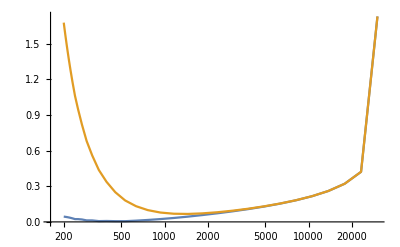

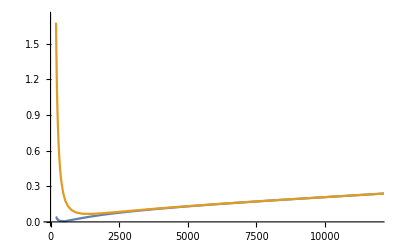

```mathematica
listaluminosita={{WmT,WpT},{WmL,WpL},{WmL,WpT},{WmT,WpL},{ZT,ZT},{ZL,ZL},{ZL,ZT},{ZT,ZL},{Wmm,Wpm},{Wmm,Wpp},{Wmp,Wpm},{Wmp,Wpp},{Zm,Zm},{Zm,Zm},{Zp,Zm},{Zp,Zp}}
listaenergie={1000,3000,10000,30000}
bins=40;
Stot=30000
minM=200;
facsc=0.5
pair=2
Tagpart1=listaluminosita[[pair,1]];
Tagpart2=listaluminosita[[pair,2]];
uno=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,facsc]
due=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,facsc]
tre=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,facsc]
rapp1=sumconst[rapp[due,uno],-1]
rapp2=sumconst[rapp[tre,uno],-1]
listaluminosita[[pair]]
ListLogLinearPlot[{rapp1,rapp2},Joined->True,InterpolationOrder->1]
ListPlot[{rapp1,rapp2},Joined->True,InterpolationOrder->1]
```

```mathematica
ListLogLinearPlot[{rapp1,rapp2},Joined->True,InterpolationOrder->]
ListPlot[{rapp1,rapp2},Joined->True,InterpolationOrder->1]
```

```mathematica
Lμmμpscale[WmT,WpT,1000,1000,1]
```

0.

Parton luminosity for a μ- <> μ+ collider as function of the partonic  invariant mass m, which also fixes the PDF factorization scale as m/2.

```mathematica
??Do
```

```mathematica
listaluminosita[[1,2]]
```

WpT

```mathematica
listaluminosita={{WmT,WpT},{WmL,WpL},{WmL,WpT},{WmT,WpL},{ZT,ZT},{ZL,ZL},{ZL,ZT},{ZT,ZL},{Wmm,Wpm},{Wmm,Wpp},{Wmp,Wpm},{Wmp,Wpp},{Zm,Zm},{Zm,Zm},{Zp,Zm},{Zp,Zp}}
listaenergie={1000,3000,10000,30000}
```

{{WmT,WpT},{WmL,WpL},{WmL,WpT},{WmT,WpL},{ZT,ZT},{ZL,ZL},{ZL,ZT},{ZT,ZL},{Wmm,Wpm},{Wmm,Wpp},{Wmp,Wpm},{Wmp,Wpp},{Zm,Zm},{Zm,Zm},{Zp,Zm},{Zp,Zp}}

{1000,3000,10000,30000}

```mathematica
Do[
joinedoption=True;
bins=40;
Stot=listaenergie[[k]];
minM=500;

Tagpart1=listaluminosita[[j,1]];
Tagpart2=listaluminosita[[j,2]];
PDFpoints=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.5];
PDFpointsscale1=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,1];
PDFpointsscale025=LμmμpNpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.25];
EVApoints=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.5];
EVAv2points=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.5];
EVAv2pointsscale1=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,1];
EVAv2pointsscale025=LμmμpEVAv2Npointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.25];
EVApointsscale1=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,1];
EVApointsscale025=LμmμpEVANpointsscale[Tagpart1,Tagpart2,minM,Stot,bins,0.25];

plotstyle={{Thick,Black},{Thick,Blue},{Thick,Red},{Dashed,Black},{DotDashed,Black},{Dashed,Red},{DotDashed,Red},{Dashed,Blue},{DotDashed,Blue}};

Ecoll=Stot/1000;
Plot1[Tagpart1,Tagpart2]=ListLogLogPlot[{PDFpoints,EVApoints,EVAv2points,PDFpointsscale1,PDFpointsscale025,EVAv2pointsscale1,EVAv2pointsscale025,EVApointsscale1,EVApointsscale025},Joined->joinedoption,PlotLegends->{"PDFs (scale=m(X)/2)","EVA only Log[Q/MV] (scale=m(X)/2)","EVA (scale=m(X)/2)","PDF (scale x 2)","PDF (scale/2)","EVA (scale x 2)","EVA (scale/2)","EVA only Log[Q/MV](scale x 2)","EVA only Log[Q/MV](scale x 2)"},PlotStyle->plotstyle,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,Frame->True,FrameLabel->{"m(X) [GeV]","L of "<>ToString[Tagpart1]<>"-"<>ToString[Tagpart2]<>" at "<>ToString[Ecoll]<>" TeV"}];
Plot2[Tagpart1,Tagpart2]=ListLogLogPlot[{rapp[PDFpoints,PDFpoints],rapp[EVApoints,PDFpoints],rapp[EVAv2points,PDFpoints],rapp[PDFpointsscale1,PDFpoints],rapp[PDFpointsscale025,PDFpoints],rapp[EVAv2pointsscale1,PDFpoints],rapp[EVAv2pointsscale025,PDFpoints],rapp[EVApointsscale1,PDFpoints],rapp[EVApointsscale025,PDFpoints]},Joined->joinedoption,PlotLegends->{"PDFs (scale=m(X)/2)","EVA only Log[Q/MV] (scale=m(X)/2)","EVA (scale=m(X)/2)","PDF (scale x 2)","PDF (scale/2)","EVA (scale x 2)","EVA (scale/2)","EVA only Log[Q/MV](scale x 2)","EVA only Log[Q/MV](scale x 2)"},PlotStyle->plotstyle,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,Frame->True,FrameLabel->{"m(X) [GeV]","Ratio over L(PDFs) for "<>ToString[Tagpart1]<>"-"<>ToString[Tagpart2]<>" at "<>ToString[Ecoll]<>" TeV"}];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>ToString[listaluminosita[[j,1]]]<>"-"<>ToString[listaluminosita[[j,2]]]<>".pdf",Plot1[listaluminosita[[j,1]],listaluminosita[[j,2]]]];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/ratios/"<>ToString[listaluminosita[[j,1]]]<>"-"<>ToString[listaluminosita[[j,2]]]<>".pdf",Plot2[listaluminosita[[j,1]],listaluminosita[[j,2]]]];
Print[{listaenergie[[k]],listaluminosita[[j,1]],listaluminosita[[j,2]]}];
,{j,1,Length[listaluminosita]},{k,1,Length[listaenergie]}
]
```

{1000,WmT,WpT}

{3000,WmT,WpT}

{10000,WmT,WpT}

{30000,WmT,WpT}

{1000,WmL,WpL}

{3000,WmL,WpL}

{10000,WmL,WpL}

{30000,WmL,WpL}

{1000,WmL,WpT}

{3000,WmL,WpT}

{10000,WmL,WpT}

{30000,WmL,WpT}

{1000,WmT,WpL}

{3000,WmT,WpL}

{10000,WmT,WpL}

{30000,WmT,WpL}

{1000,ZT,ZT}

{3000,ZT,ZT}

{10000,ZT,ZT}

{30000,ZT,ZT}

{1000,ZL,ZL}

{3000,ZL,ZL}

{10000,ZL,ZL}

{30000,ZL,ZL}

{1000,ZL,ZT}

{3000,ZL,ZT}

{10000,ZL,ZT}

{30000,ZL,ZT}

{1000,ZT,ZL}

{3000,ZT,ZL}

{10000,ZT,ZL}

{30000,ZT,ZL}

{1000,Wmm,Wpm}

{3000,Wmm,Wpm}

{10000,Wmm,Wpm}

{30000,Wmm,Wpm}

{1000,Wmm,Wpp}

{3000,Wmm,Wpp}

{10000,Wmm,Wpp}

{30000,Wmm,Wpp}

{1000,Wmp,Wpm}

{3000,Wmp,Wpm}

{10000,Wmp,Wpm}

{30000,Wmp,Wpm}

{1000,Wmp,Wpp}

{3000,Wmp,Wpp}

{10000,Wmp,Wpp}

{30000,Wmp,Wpp}

{1000,Zm,Zm}

{3000,Zm,Zm}

{10000,Zm,Zm}

{30000,Zm,Zm}

{1000,Zm,Zm}

{3000,Zm,Zm}

{10000,Zm,Zm}

{30000,Zm,Zm}

{1000,Zp,Zm}

{3000,Zp,Zm}

{10000,Zp,Zm}

{30000,Zp,Zm}

{1000,Zp,Zp}

{3000,Zp,Zp}

{10000,Zp,Zp}

{30000,Zp,Zp}

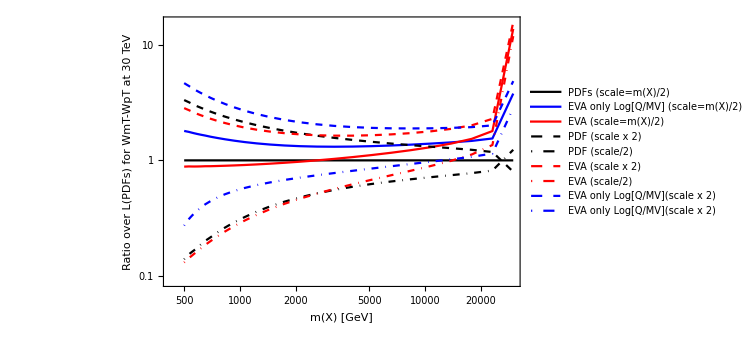
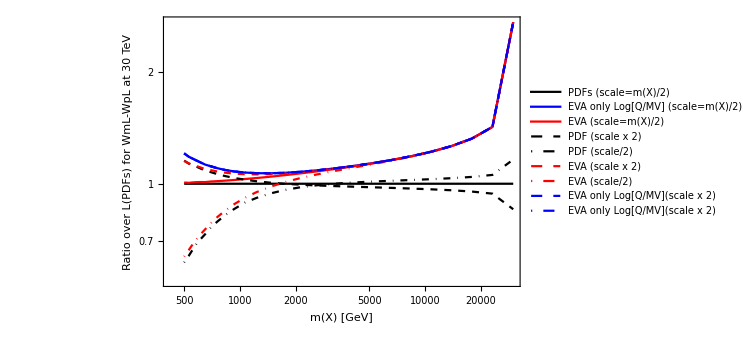
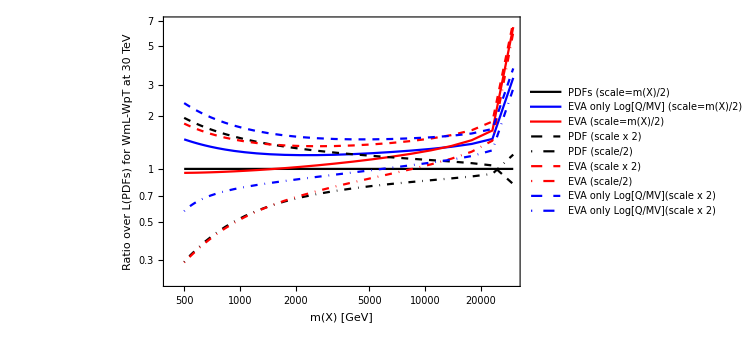
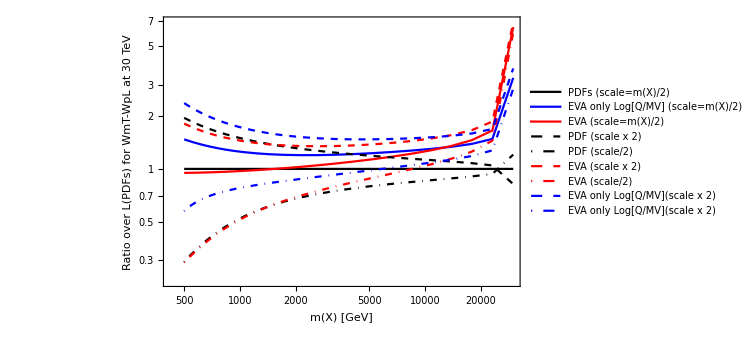
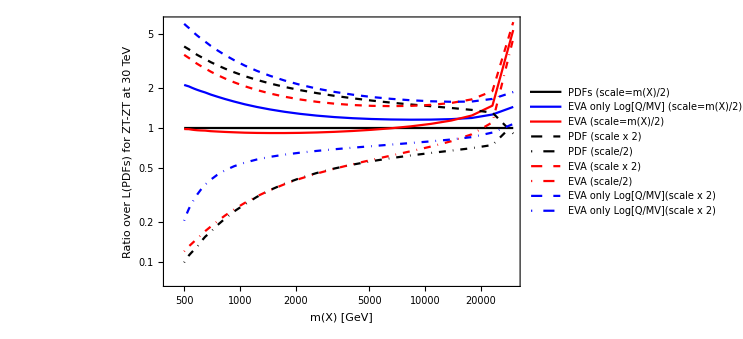
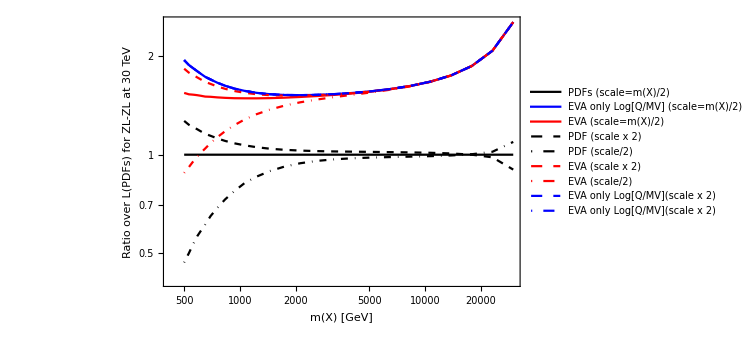
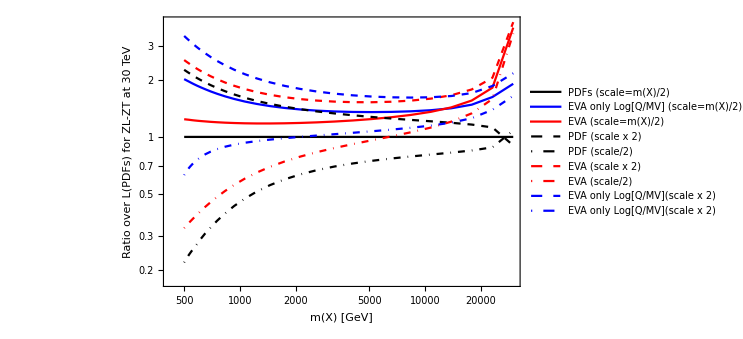
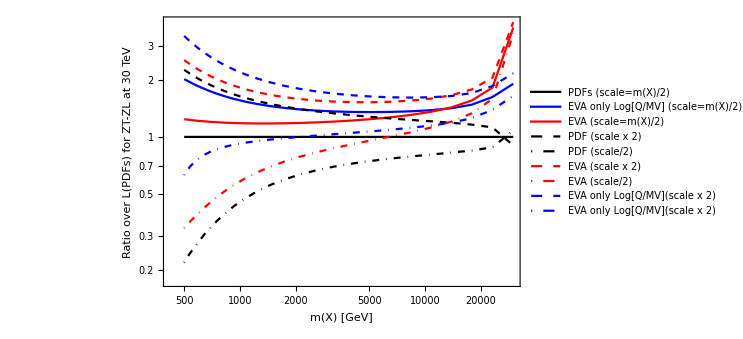
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot2[listaluminosita[[i,1]],listaluminosita[[i,2]]],{i,1,Length[listaluminosita]}]
```

```mathematica
(*Do[Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>ToString[listaluminosita[[i,1]]]<>"-"<>ToString[listaluminosita[[i,2]]]<>".pdf",Plot1[listaluminosita[[i,1]],listaluminosita[[i,2]]]],{i,1,Length[listaluminosita]}]
Do[Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/ratios/"<>ToString[listaluminosita[[i,1]]]<>"-"<>ToString[listaluminosita[[i,2]]]<>".pdf",Plot1[listaluminosita[[i,1]],listaluminosita[[i,2]]]],{i,1,Length[listaluminosita]}]*)
```

```mathematica
(*

Se METTO Wp nel mu-, EVA va a zero

PDFpoints=LμmμpNpoints[WpT,WmT,minM,Stot,bins]
EVApoints=LμmμpEVANpoints[WpT,WmT,minM,Stot,bins]
EVAv2points=LμmμpEVAv2Npoints[WpT,WmT,minM,Stot,bins]

*)
```

```mathematica
(*Riredefinisco lo scan a step lineari*)
```

```mathematica
LμmμpNpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),Lμmμpscale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
LμmμpEVANpointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVAscale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
LμmμpEVAv2Npointsscale[part1_,part2_,mμμ_,sqrts0_,Npoints_,muovermμμ_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVAv2scale[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0,muovermμμ]},{i,1,Npoints}]
```

```mathematica
joinedoption=True
```

True

```mathematica
True
Do[
bins=40;
Stot=listaenergie[[k]];
minM=200;


plotWmWpandWpWm=ListLogPlot[{LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WpT,WmT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpL,minM,Stot,bins,0.5],LμmμpNpointsscale[WpL,WmL,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WpT,WmT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WmL,WpL,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WpL,WmL,minM,Stot,bins,0.5]},(*PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}*)
PlotStyle->{Black,Orange,Brown,Red,{Dashed,Black},{Dashed,Orange},{Dashed,Brown},{Dashed,Red}}
(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity (dashed with EVA)"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W+_T W-_T","W-_0 W+_0","W+_0 W-_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotWmWpandWpWm.pdf",plotWmWpandWpWm];

plotWWpolTand0=ListLogPlot[{LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmT,WpL,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpL,minM,Stot,bins,0.5],
LμmμpEVAv2Npointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WmL,WpT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WmT,WpL,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[WmL,WpL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,{Dashed,Black},{Dashed,Orange},{Dashed,Brown},{Dashed,Red}}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity (dashed with EVA)"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W-_0 W+_T","W-_T W+_0","W-_0 W+_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotWWpolTand0.pdf",plotWWpolTand0];

plotWWpolRandL=ListLogPlot[{LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmm,Wpm,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmp,Wpp,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmp,Wpm,minM,Stot,bins,0.5],LμmμpNpointsscale[Wmm,Wpp,minM,Stot,bins,0.5],
LμmμpEVAv2Npointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Wmm,Wpm,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Wmp,Wpp,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Wmp,Wpm,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Wmm,Wpp,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],{Dashed,Black},{Dashed,Orange},{Dashed,Brown},{Dashed,Red},{Dashed,Darker[Green]}},(*PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}*)(*,PlotRange->{{0.00099,1},{0.001,100}}*)Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity (dashed with EVA)"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W-_L W+_L","W-_R W+_R","W-_R W+_L","W-_L W+_R"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotWWpolRandL.pdf",plotWWpolRandL];

plotZZpolTand0=ListLogPlot[{LμmμpNpointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[ZL,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[ZT,ZL,minM,Stot,bins,0.5],LμmμpNpointsscale[ZL,ZL,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[ZL,ZT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[ZT,ZL,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[ZL,ZL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,{Dashed,Black},{Dashed,Orange},{Dashed,Brown},{Dashed,Red}}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity (dashed with EVA)"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"Z_T Z_T","Z_0 Z_T","Z_T Z_0","Z_0 Z_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotZZpolTand0.pdf",plotZZpolTand0];

plotZZpolRandL=ListLogPlot[{LμmμpNpointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[Zm,Zm,minM,Stot,bins,0.5],LμmμpNpointsscale[Zp,Zp,minM,Stot,bins,0.5],LμmμpNpointsscale[Zp,Zm,minM,Stot,bins,0.5],LμmμpNpointsscale[Zm,Zp,minM,Stot,bins,0.5],
LμmμpEVAv2Npointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Zm,Zm,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Zp,Zp,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Zp,Zm,minM,Stot,bins,0.5],LμmμpEVAv2Npointsscale[Zm,Zp,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],{Dashed,Black},{Dashed,Orange},{Dashed,Brown},{Dashed,Red},{Dashed,Darker[Green]}}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity (dashed with EVA)"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"Z_T Z_T","Z_L Z_L","Z_R Z_R","Z_R Z_L","Z_L Z_R"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotZZpolRandL.pdf",plotZZpolRandL];


plotgammaWZ=ListLogPlot[{LμmμpNpointsscale[γ,γ,minM,Stot,bins,0.5],LμmμpNpointsscale[WmT,WpT,minM,Stot,bins,0.5],LμmμpNpointsscale[WmL,WpL,minM,Stot,bins,0.5],LμmμpNpointsscale[ZT,ZT,minM,Stot,bins,0.5],LμmμpNpointsscale[ZL,ZL,minM,Stot,bins,0.5]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"m(X) [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[12,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"γγ","W-_T W+_T","W-_0 W+_0","Z_T Z_T","Z_0 Z_0"},PlotLabel->"PDFs (scale=m(X)/2) Luminosity at "<>ToString[Stot/1000]<>" TeV : mu- mu+",Joined->joinedoption];
Export["/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotLumi/"<>ToString[Stot/1000]<>"TeV/lumis/"<>"plotgammaWZ.pdf",plotgammaWZ];

,{k,1,Length[listaenergie]}]
```

True

NIntegrate::inumr: The integrand ((μEVApartv2[Wpm,100.,1/(25 x)]+μEVApartv2[Wpp,100.,1/(25 x)]) (μEVApartv2[Wpm,100.,x]+μEVApartv2[Wpp,100.,x]))/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/25,1}}.

NIntegrate::inumr: The integrand ((μEVApartv2[Wpm,110.256,1849/(38025 x)]+μEVApartv2[Wpp,110.256,1849/(38025 x)]) (μEVApartv2[Wpm,110.256,x]+μEVApartv2[Wpp,110.256,x]))/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{1849/38025,1}}.

NIntegrate::inumr: The integrand ((μEVApartv2[Wpm,120.513,2209/(38025 x)]+μEVApartv2[Wpp,120.513,2209/(38025 x)]) (μEVApartv2[Wpm,120.513,x]+μEVApartv2[Wpp,120.513,x]))/x has evaluated to non-numerical values for all sampling points in the region with boundaries {{2209/38025,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
(*

μbEVA has to be defined before



LμmμpEVA[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μEVApart[part1,mμμ/2][x]μbEVApart[part2,mμμ/2][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]

LμmμpEVANpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVA[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0]},{i,1,Npoints}]*)
```